## Introduction

Making movies for ring swarmalator model with K_j

## All states at once

LinkObject::linkw: Unable to write data to closed link ….

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -pacletreadonly -wstp,1532,14].

LinkObject::linkd: Unable to communicate with closed link LinkObject['/Applications/Mathematica.app/Contents/MacOS/WolframKernel' -subkernel -noinit -pacletreadonly -wstp,1533,15].

Parallel`Developer`ConnectKernel::failinit: 2 of 6 kernels failed to initialize.

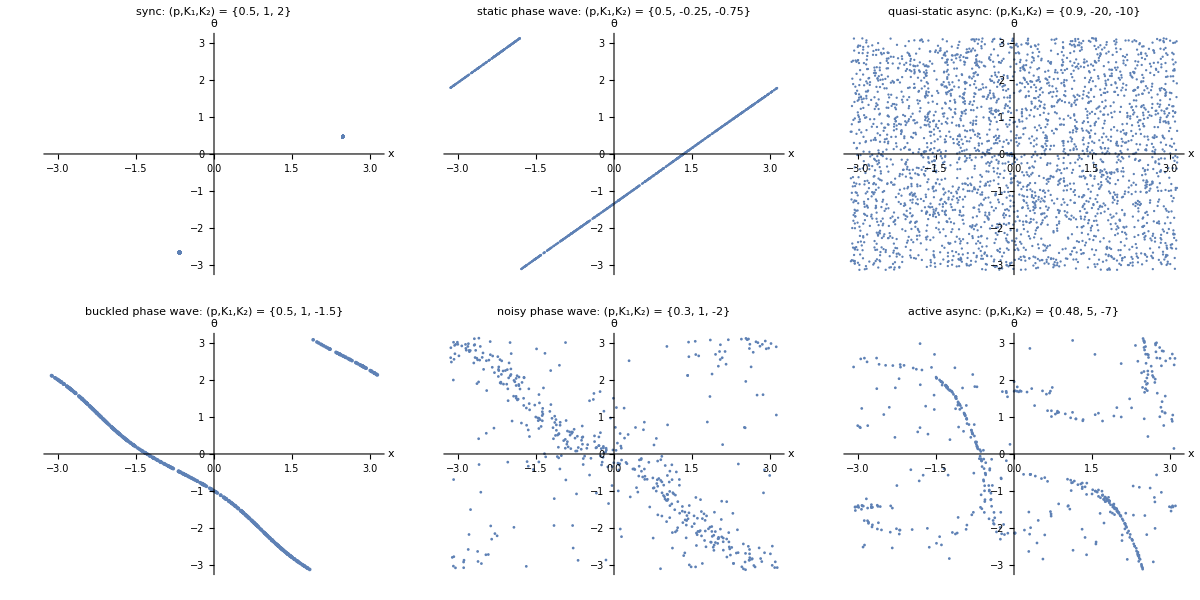

```mathematica
pars={
{0.5,1,2,500,"sync"},
{0.5,-0.25,-0.75,1000,"static phase wave"},
{0.9,-20,-10,3000,"quasi-static async"},
{0.5,1,-1.5,500,"buckled phase wave"},
{0.3,1,-2,500,"noisy phase wave"},
{0.48,5,-7,500,"active async"}
};

allSlides=ParallelTable[
(*Make slides*)
SeedRandom[0];
{dt,T}={0.1,100};  (*dt = timestep, n = number of swarmalators*)
{p,k1,k2,n,state}=par;
js=Table[1,{i,1,n}];
ks =Table[If[i≤Floor[p*n],k1,k2],{i,1,n}];
{z0,znew}={Table[RandomReal[{0,2 π}],{i,1,2},{j,1,n}],ConstantArray[0,{2,n}]};
results={};
{t,NT}={0,Floor[T/dt]} ; (*T = number of timesteps*)
slides={};
While[t<NT,
znew=rk4[z0,rhs,dt,js,ks];
z0=znew;t++;
fig=plotResultsSingle[znew,J,k,Δ,state<>": (p,K_1,K_2) = "<>ToString[{p,k1,k2}]];
AppendTo[slides,fig]
];
slides,
{par,pars}
];
Grid[{allSlides[[1;;3,-1]],allSlides[[4;;-1,-1]]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
fullSlides=Table[Grid[{allSlides[[1;;3,t]],allSlides[[4;;-1,t]]}],{t,1,Dimensions[allSlides][[2]]}];
Export["movies/all-states.mov",fullSlides]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

movies/all-states.mov

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real,1},{k,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,inverseDist,xtemp,ytemp,thetatemp,rep,A,B,C,n1,vel=ConstantArray[0.0,{2,n}]},
{A,B,C,n1}={1,1,10,1};
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
If[j≠i,
xji=z[[1,j]]-z[[1,i]];
thetaji=z[[2,j]]-z[[2,i]];
xtemp=J[[j]]*Sin[xji] Cos[thetaji];
thetatemp=k[[j]]*Sin[thetaji] Cos[xji];
vel[[1,i]]+=xtemp;
vel[[2,i]]+=thetatemp;
]
];
];
vel/N[n]
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];

findWs[z_]:=Block[{Wp,Wm,i,numOsc},
{Wp,Wm}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Wp+=Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Wm+=Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Wp/numOsc,Wm/numOsc}]
];

findVs[z_,j_,k_]:=Block[{Upos,Um,Vp,Vm,i,numOsc},
{Upos,Um,Vp,Vm}={0,0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Upos+=j[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Um+=j[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
Vp+=k[[i]]*Exp[ⅈ (z[[1,i]]+z[[2,i]])];
Vm+=k[[i]]*Exp[ⅈ (z[[1,i]]-z[[2,i]])];
];
Return[{Upos/numOsc,Um/numOsc,Vp/numOsc,Vm/numOsc}]
];

findRs[z_]:=Block[{Z,Y,i,numOsc},
{Z,Y}={0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
Y+=Exp[ⅈ (z[[1,i]])];
Z+=Exp[ⅈ (z[[2,i]])];
];
Return[{Y/numOsc,Z/numOsc}]
]

plotResults[z_,js_,ks_]:=Block[{colors,Wp,Wm,Vp,Vm,Rx,Rtheta,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
{Upos,Um,Vp,Vm}=findVs[z,js,ks];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],
Magenta,Point[{Upos//Re,Upos//Im}],Black,Text["U_+",{Upos//Re,Upos//Im}],
Magenta,Point[{Um//Re,Um//Im}],Black,Text["U_-",{Um//Re,Um//Im}],
Cyan,Point[{Vp//Re,Vp//Im}],Black,Text["V_+",{Vp//Re,Vp//Im}],
Cyan,Point[{Vm//Re,Vm//Im}],Black,Text["V_-",{Vm//Re,Vm//Im}],

(*Domain*)
Black,Circle[{0,0},1]
},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium];
p2=ListPlot[{Mod[z[[1,All]],2π],Mod[z[[2,All]],2π]}ᵀ,PlotRange->{{0,2π},{0,2π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{Mod[z[[1,All]]+z[[2,All]],2π],Mod[z[[1,All]]-z[[2,All]],2π]}ᵀ,PlotRange->{{0π,2π},{0π,2π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];


eulerStep1D[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,vel},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
vel=F[z,n,J,k];
znew=z+dt*vel;
Return[znew]
];

rk4[z_,F_,dt_,J_,k_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,k];
k2=F[z+dt/2 k1,n,J,k];
k3=F[z+dt/2 k2,n,J,k];
k4=F[z+dt k3,n,J,k];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findMeanV[znew_,z_,dt_]:=Block[{v},
v=(znew-z)/dt;
v=(v[[1,All]]^2+v[[2,All]]^2)^(1/2);
Return[Mean[v]]
];

findBuckleWidth[znew_]:=Block[{x,θ,ξ,η,L,Wp,Wm},
{x,θ}=znew;
{ξ,η}={x+θ,x-θ}//mod;
{Wp,Wm}=findWs[znew];
If[Abs[Wp]<Abs[Wm],{ξ,η}={η,ξ}];
L=Max[ξ]-Min[ξ];
Return[L]
];

plotResultsCustom[z_,p_,K1_,K2_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[2,All]],2π]-1)/(2π)+380);
{Wp,Wm}=findWs[z];
{Rx,Rtheta}=findRs[z];
{Upos,Um,Vp,Vm}=findVs[z,js,ks];
p1=Graphics[{

(*Swarmalators*)
PointSize[0.02],Point[{Cos[z[[1,All]]],Sin[z[[1,All]]]}ᵀ,VertexColors->colors],

(*Order parameters*)
PointSize[0.05],
Green,Point[{Wp//Re,Wp//Im}],Black,Text["W_+",{Wp//Re,Wp//Im}],
Green,Point[{Wm//Re,Wm//Im}],Black,Text["W_-",{Wm//Re,Wm//Im}],
Magenta,Point[{Upos//Re,Upos//Im}],Black,Text["U_+",{Upos//Re,Upos//Im}],
Magenta,Point[{Um//Re,Um//Im}],Black,Text["U_-",{Um//Re,Um//Im}],
Cyan,Point[{Vp//Re,Vp//Im}],Black,Text["V_+",{Vp//Re,Vp//Im}],
Cyan,Point[{Vm//Re,Vm//Im}],Black,Text["V_-",{Vm//Re,Vm//Im}],

(*Domain*)
Black,Circle[{0,0},1]

},
PlotRange->{{-1.25,1.25},{-1.25,1.25}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"x","y"},LabelStyle->20,ImageSize->Medium,PlotLabel->Style[label,15,Black]];
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]}];
p3=ListPlot[{z[[1,All]]+z[[2,All]],z[[1,All]]-z[[2,All]]}ᵀ//mod,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["ξ",15],Style["η",15]}];
Return[Grid[{{p1,p2,p3}}]
]
];

plotResultsSingle[z_,J_,K_,Δ_,label_]:=Block[{colors,Wp,Wm,p1,p2,p3},
p2=ListPlot[{z[[1,All]]//mod,z[[2,All]]//mod}ᵀ,
PlotRange->{{-π,π},{-π,π}},ImageSize->Medium,AxesLabel->{Style["x",15],Style["θ",15]},PlotLabel->Style[label,15,Black]];
Return[p2]
];
```